## Test Problem 4

A couple of implementations of the A function.  Second one is more Julia friendly

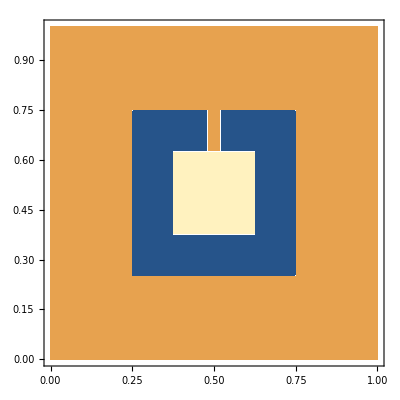

```mathematica
A[{x_,y_}]:= Module[{a=0.25,b=0.125, c=1/50},
Which[
Or[x<a,x>1-a,y<a,y>1-a], 10,
And[Abs[x-1/2]≤c,0.5+b≤y],10,
And[ Abs[x-1/2]≤b, Abs[y-1/2]≤b], 20,
True, 1]]
ContourPlot[A[{x,y}],{x,0,1},{y,0,1},
PlotPoints->50]
```

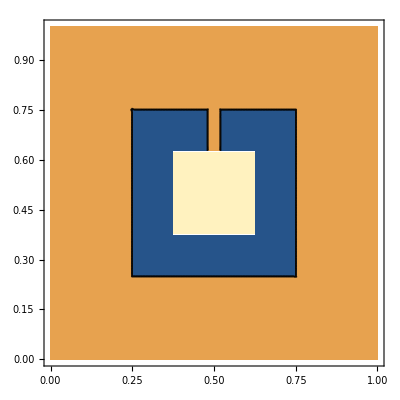

```mathematica
Clear[A]
A[{x_,y_}]:= Module[{a=0.25,b=0.125, c=1/50},
If[ Or[x<a,x>1-a,y<a,y>1-a],Return[10]];
If[  And[Abs[x-1/2]≤c,0.5+b≤y],Return[10]];
If[And[ Abs[x-1/2]≤b, Abs[y-1/2]≤b], Return[20],Return[1]]
]
ContourPlot[A[{x,y}],{x,0,1},{y,0,1},
PlotPoints->50]
```

## NDSolve Matrices

Here is how to find and extract a matrix from Mathematica for a PDE.

```mathematica
Needs["NDSolve`FEM`"]
Ω=ToNumericalRegion[Rectangle[{0,0},{1,1}]];
{state}=NDSolve`ProcessEquations[{-Laplacian[u[x,y],{x,y}]==1,DirichletCondition[u[x,y]==0,True]},u,{x,y}∈Ω];
FEMData=state["FiniteElementData"];
sd=NDSolve`SolutionData[{"Space"}->{Ω}];
DiscretizedData=NDSolve`FEM`DiscretizePDE[FEMData["PDECoefficientData"],FEMData["FEMMethodData"],sd, "Stationary",
"AssembleSystemMatrices"->True]
DiscretizedData["Properties"]
M=DiscretizedData["MassMatrix"];
A=DiscretizedData["StiffnessMatrix"]
Eigenvalues[A,-12]
```

DiscretizedPDEData[<1281>]

{All,DampingElements,DampingMatrix,LoadElements,LoadVector,MassElements,MassMatrix,Properties,StiffnessElements,StiffnessMatrix,SystemElements,SystemMatrices}

SparseArray[…]

{0.0704579,0.0658913,0.0658913,0.0572288,0.0357637,0.0357637,0.029659,0.0295427,0.0143835,0.00744396,0.00744396,-2.75028×10^-17}

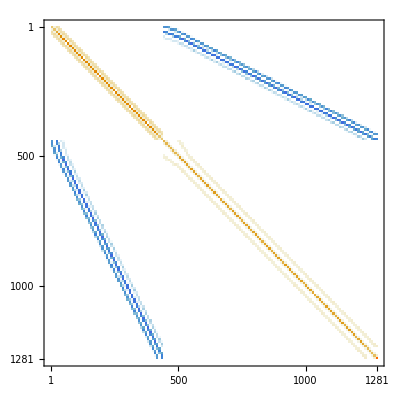

```mathematica
MatrixPlot[A]
```

# PDE Test Problems Van Der Vorst

## Reference

@article{doi:10.1137/0913035,
author = {van der Vorst, H. A.},
title = {Bi-CGSTAB: A Fast and Smoothly Converging Variant of Bi-CG for the Solution of Nonsymmetric Linear Systems},
journal = {SIAM Journal on Scientific and Statistical Computing},
volume = {13},
number = {2},
pages = {631-644},
year = {1992},
doi = {10.1137/0913035},
URL = {    https://doi.org/10.1137/0913035
},
eprint = {   https://doi.org/10.1137/0913035},
abstract = { Recently the Conjugate Gradients-Squared (CG-S) method has been proposed as an attractive variant of the Bi-Conjugate Gradients (Bi-CG) method. However, it has been observed that CG-S may lead to a rather irregular convergence behaviour, so that in some cases rounding errors can even result in severe cancellation effects in the solution. In this paper, another variant of Bi-CG is proposed which does not seem to suffer from these negative effects. Numerical experiments indicate also that the new variant, named Bi-CGSTAB, is often much more efficient than CG-S. }
}

## Test 1: -Δu=f on Ω=[0,1]^2 Homogeneous Dirichlet BC 150×150 grid

The points i=1:n  and j=1:n are all interior points. The fully interior points i=2:n-1 and i=2:n-1 use the standard five point stencil.  The boundary adjacent points i=1,n and j=1,n simply drop the coefficients associated with the boundary value that is zeroed by the homogeneous Dirichlet condition.

```mathematica
n=50;
Δx=Δy=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A1=SparseArray[{},{m,m}];
Do[
k=ijTok[n][i,j];
A1⟦k,k⟧=4.0;
If[1≤i+1≤n,A1⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A1⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A1⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A1⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
A1=A1/Δx^2;
```

Check the matrix is consistent with the stated PDE problem.  True applies the boundary condition on all boundaries.

```mathematica
Eigenvalues[A1,-10]
NDEigenvalues[{
-Laplacian[u[x,y],{x,y}],
DirichletCondition[u[x,y]==0,True]
},
u[x,y],
 {x,y}∈Rectangle[{0,0},{1,1}],10
]
```

{166.983,166.983,128.002,128.002,98.4404,98.4404,78.857,49.295,49.295,19.733}

{19.7392,49.3486,49.3486,78.9579,98.7021,98.7021,128.311,128.311,167.817,167.817}

Looks pretty close.  To get closer make n larger!

## Test 2: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Mixed Neumann-Dirichlet Boundary Conditions

The plan is to build up to this slowly.  There are two new complications: boundary conditions and the function D.

### Test 1.8: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Neumann BC on y=0 and Dirichlet on the other three sides 150×150 grid With D=1.

The points i=1:n  and j=1:n are all interior points. The fully interior points i=2:n-1 and i=2:n-1 use the standard five point stencil.  The Dirichlet boundary adjacent points i=1,n and j=n simply drop the coefficients associated with the boundary value that is zeroed by the homogeneous Dirichlet condition.  The Neumann boundary adjacent points j=1 simply burn the (admittedly lower order) one sided difference implementation of the homogeneous Neumann condition 
	u_(i,0)=u_(i,1)
into the standard stencil 
	  |   | u_(i,2) |   |  
  |   | ↕ |   |  
u_(i-1,1) | ↔ | -4 u_(i,1) | ↔ | u_(i+1,1)
  |   | ↕ |   |  
  |   | u_(i,0) |   |  
to get
	  |   | u_(i,2) |   |  
  |   | ↕ |   |  
u_(i-1,1) | ↔ | -3 u_(i,1) | ↔ | u_(i+1,1)
  |   | ↕ |   |  
  |   | □ |   |  
This is relatively easy to implement

```mathematica
n=100;
Δx=Δy=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A18=SparseArray[{},{m,m}];
(* Interior and Dirichlet Conditions *)
Do[
k=ijTok[n][i,j];
A18⟦k,k⟧=4.0;
If[1≤i+1≤n,A18⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A18⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A18⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A18⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,2,n}]
(* Neumann Condition on y=0 i.e j=1 *)
j=1;
Do[
k=ijTok[n][i,j];
A18⟦k,k⟧=3.0;
If[1≤i+1≤n,A18⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A18⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A18⟦k,ijTok[n][i,j+1]⟧=-1.0],
{i,1,n}
]
A18=A18/Δx^2
```

SparseArray[…]

Lets check that this is correct.  Looks pretty good again. 
I now have to call out the  boundaries I want.  If I do not call boundary conditions on a piece of the boundary “natural” i.e. homogeneous Neumann conditions are automatic!

```mathematica
Eigenvalues[A18,-10]
NDEigenvalues[{
-Laplacian[u[x,y],{x,y}],
DirichletCondition[u[x,y]==0,y==1],
DirichletCondition[u[x,y]==0,x==0],
DirichletCondition[u[x,y]==0,x==1]
},
u[x,y],
 {x,y}∈Rectangle[{0,0},{1,1}],10
]
```

{151.031,131.856,111.186,101.734,91.254,72.1374,61.8897,41.9576,32.2928,12.3608}

{12.337,32.0763,41.9464,61.6857,71.5567,91.2999,101.166,111.039,130.787,150.52}

The matrix is symmetric!

```mathematica
Norm[A18-A18ᵀ,"Frobenius"]
```

0.

### Test 1.85: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Dirichlet BC on y=0 and Neuman on the other three sides 150×150 grid With D=1.

The Neumann boundary stencil is 
	  |   | u_(i,2) |   |  
  |   | ↕ |   |  
u_(i-1,1) | ↔ | -3 u_(i,1) | ↔ | u_(i+1,1)
  |   | ↕ |   |  
  |   | □ |   |  
A similar argument gives the Neuman-Neuman corner stencil
	  |   | u_(1,2) |   |  
  |   | ↕ |   |  
□ | ↔ | -2 u_(1,1) | ↔ | u_(2,1)
  |   | ↕ |   |  
  |   | □ |   |  
This is getting a bit annoying.

```mathematica
Clear[i,j]
```

```mathematica
n=75;
Δx=Δy=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A185=SparseArray[{},{m,m}];
(* Interior and Dirichlet Conditions on all sides *)
Do[
k=ijTok[n][i,j];
A185⟦k,k⟧=4.0;
If[1≤i+1≤n,A185⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A185⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A185⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A185⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
(* Modifying to give Neumann *)
(* All I need to do is replace the 4.0 with 3.0 along the Neumann Edges *)
(* Neumann edges are i=1,n and j=n *)
(* First edge i=1 *)
Do[
k=ijTok[n][1,j];
A185⟦k,k⟧=3.0,
{j,1,n}]
(* Now edge i=n *)
Do[
k=ijTok[n][n,j];
A185⟦k,k⟧=3.0,
{j,1,n}]
(* Now Edge j=n *)
Do[
k=ijTok[n][i,n];
A185⟦k,k⟧=3.0,
{i,1,n}]
(* Sadly we are not quite done because the Neumann-Neumann corners *)
(* {i,j}={1,n} and {i,j}={n,n} should be special with a 2.0 rather than a 3.0 *)
k=ijTok[n][1,n];
A185⟦k,k⟧=2.0;
k=ijTok[n][n,n];
A185⟦k,k⟧=2.0;

A185=A185/Δx^2
```

SparseArray[…]

Lets check that this is correct. 
I now have to call out the  boundaries I want.  If I do not call boundary conditions on a piece of the boundary “natural” i.e. homogeneous Neumann conditions are automatic! Again it is pretty clear that this is correct!

```mathematica
Eigenvalues[A185,-10]
NDEigenvalues[{
-Laplacian[u[x,y],{x,y}],
DirichletCondition[u[x,y]==0,y==0]
},
u[x,y],
 {x,y}∈Rectangle[{0,0},{1,1}],10
]
```

{102.963,93.5911,72.5815,63.0089,62.4484,43.0146,32.6275,22.4944,12.6332,2.5001}

{2.4674,12.337,22.2067,32.0763,41.9464,61.6857,61.687,71.5567,91.2999,101.166}

The matrix is still symmetric!

```mathematica
Norm[A185-A185ᵀ,"Frobenius"]
```

0.

### Test 1.9: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Dirichlet Conditions on all sides

The key to thinking about the differencing for the non constant function is to just start making the recipe as before 
	(D(x,y)u_x)_x≈(D(x,y)((u(x+Δx/2,y)-u(x-Δx/2,y))/Δx))_x
and keep going
	(D(x,y)u_x)_x≈((D(x+Δx/2,y)((u(x+Δx/2+Δx/2,y)-u(x-Δx/2+Δx/2,y))/Δx)-D(x-Δx/2,y)((u(x+Δx/2-Δx/2,y)-u(x-Δx/2-Δx/2,y))/Δx))/Δx)
and then tidy up carefully
	(D(x,y)u_x)_x≈((D(x+Δx/2,y)((u(x+Δx,y)-u(x,y))/Δx)-D(x-Δx/2,y)((u(x,y)-u(x-Δx,y))/Δx))/Δx)
and then clean up the fractions 
	(D(x,y)u_x)_x≈(D(x+Δx/2,y)(u(x+Δx,y)-u(x,y))-D(x-Δx/2,y)(u(x,y)-u(x-Δx,y)))/Δx^2
and finally distribute the signs to get
	(D(x,y)u_x)_x≈(D(x+Δx/2,y)(u(x+Δx,y) - (D(x+Δx/2,y) + D(x-Δx/2,y))u(x,y) + D(x-Δx/2,y)u(x-Δx,y))/Δx^2.
The last step is to make some obvious definitions to help remember this 
	(D(x,y)u_x)_x|_(i,j)≈(D_(i+1/2,j)u_(i+1,j) - (D_(i+1/2,j) + D_(i-1/2,j))u_(i,j) + D_(i-1/2,j)u_(i-1,j))/Δx^2.
Not surprisingly, the y derivative version is 
	(D(x,y)u_y)_y|_(i,j)≈(D_(i,j+1/2)u_(i,j+1) - (D_(i,j+1/2) + D_(i,j-1/2))u_(i,j) + D_(i,j-1/2)u_(i,j-1))/Δy^2.	 
Adding the two together gives an approximation to the desired PDE.  Again I get reasonable agreement with the built in FE solver.

```mathematica
n=250;
Δx=Δy=1.0/(n+1);
DFun[x_,y_]:= If[And[0.1≤x≤0.9,0.1≤y≤0.9],1000.0,1.0]
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A19=SparseArray[{},{m,m}];
(* Interior and Dirichlet Conditions *)
Do[
k=ijTok[n][i,j];
A19⟦k,k⟧=(
DFun[Δx(i+1/2),Δy j]+DFun[Δx(i-1/2),Δy j]+
DFun[Δx i,Δy (j+1/2)]+DFun[Δx i,Δy (j-1/2)]);
If[1≤i+1≤n,A19⟦k,ijTok[n][i+1,j]⟧=-DFun[Δx (i+1/2),Δy j ]];
If[1≤i-1≤n,A19⟦k,ijTok[n][i-1,j]⟧=-DFun[Δx (i-1/2),Δy j ]];
If[1≤j+1≤n,A19⟦k,ijTok[n][i,j+1]⟧=-DFun[Δx i,Δy (j+1/2)]];
If[1≤j-1≤n,A19⟦k,ijTok[n][i,j-1]⟧=-DFun[Δx i,Δy(j-1/2)]],
{i,1,n},
{j,1,n}];
A19=A19/Δx^2;

NDEigenvalues[{
-Div[DFun[x,y]*Grad[u[x,y],{x,y}],{x,y}],
DirichletCondition[u[x,y]==0,True]
},
u[x,y],
 {x,y}∈Rectangle[{0,0},{1,1}],10
]
Eigenvalues[A19,-10]
```

{45.6325,922.857,922.857,924.99,951.81,1004.09,1006.61,1006.61,1044.89,1057.27}

{1072.02,1055.48,1043.77,1005.33,1003.25,938.616,913.362,911.55,911.55,45.6535}

The matrix is still symmetric!

```mathematica
Norm[A19-A19ᵀ,"Frobenius"]
```

0.

### Test 2: -div(D(x,y)∇u)=f on Ω=[0,1]^2 Dirichlet Condition on y=0 Neumann on all other sides

All I have to do is put the pieces together. Provided n>10 the boundary adjacent points have

```mathematica
n=150;
Δx=Δy=1.0/(n+1);
DFun[x_,y_]:= If[And[0.1≤x≤0.9,0.1≤y≤0.9],1000.0,1.0]
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A2=SparseArray[{},{m,m}];
(* Interior and Dirichlet Conditions *)
Do[
k=ijTok[n][i,j];
A2⟦k,k⟧=(
DFun[Δx(i+1/2),Δy j]+DFun[Δx(i-1/2),Δy j]+
DFun[Δx i,Δy (j+1/2)]+DFun[Δx i,Δy (j-1/2)]);
If[1≤i+1≤n,A2⟦k,ijTok[n][i+1,j]⟧=-DFun[Δx (i+1/2),Δy j ]];
If[1≤i-1≤n,A2⟦k,ijTok[n][i-1,j]⟧=-DFun[Δx (i-1/2),Δy j ]];
If[1≤j+1≤n,A2⟦k,ijTok[n][i,j+1]⟧=-DFun[Δx i,Δy (j+1/2)]];
If[1≤j-1≤n,A2⟦k,ijTok[n][i,j-1]⟧=-DFun[Δx i,Δy(j-1/2)]],
{i,1,n},
{j,1,n}];
(* Modifying to give Neumann *)
(* All I need to do is replace the diagonal value *) 
(*
DFun[Δx(i+1/2),Δy j]+DFun[Δx(i-1/2),Δy j]+
DFun[Δx i,Δy (j+1/2)]+DFun[Δx i,Δy (j-1/2)]) *)
(* with the correct Diagonal value along the Neumann Edges *)
(* Neumann edges are i=1,n and j=n *)
(* First edge i=1 *)
Do[
i=1;
k=ijTok[n][i,j];
A2⟦k,k⟧=3.0,
{j,1,n}]
(* Now edge i=n *)
Do[
i=n;
k=ijTok[n][i,j];
A2⟦k,k⟧=3.0,
{j,1,n}]
(* Now Edge j=n *)
Do[
j=n;
k=ijTok[n][i,j];
A2⟦k,k⟧=3.0,
{i,1,n}]
(* Sadly we are not quite done because the Neumann-Neumann corners *)
(* {i,j}={1,n} and {i,j}={n,n} should be special with a 2.0 rather than a 3.0 *)
k=ijTok[n][1,n];
A185⟦k,k⟧=2.0;
k=ijTok[n][n,n];
A185⟦k,k⟧=2.0;


A2=A2/Δx^2;

NDEigenvalues[{
-Div[DFun[x,y]*Grad[u[x,y],{x,y}],{x,y}],
DirichletCondition[u[x,y]==0,y==0]
},
u[x,y],
 {x,y}∈Rectangle[{0,0},{1,1}],10
]
Eigenvalues[A2,-10]
```

{10.0904,163.819,174.828,256.578,258.087,289.056,291.232,306.601,313.564,346.036}

{1074.24,1058.05,1046.64,1008.08,1006.17,936.674,911.952,910.232,910.232,45.7108}

The matrix is still symmetric!

```mathematica
Norm[A2-A2ᵀ,"Frobenius"]
```

0.

## Test 3: -div(D(x,y)∇u)+((au)_x+a u_x)/2=1 on Ω=[0,1]^2 Δx=Δy=1/201 a=20exp(3.5 (x^2+y^2)) Dirichlet BC

The interior points i,j=1:n use the standard five point stencil.  This one I am just going to build all the entries at one go.  The stencil for the Laplacian is 
	(D_(i+1/2,j)u_(i+1,j) - (D_(i+1/2,j) + D_(i-1/2,j))u_(i,j) + D_(i-1/2,j)u_(i-1,j))/Δx^2+(D_(i,j+1/2)u_(i,j+1) - (D_(i,j+1/2) + D_(i,j-1/2))u_(i,j) + D_(i,j-1/2)u_(i,j-1))/Δy^2
as above.  The stencil for  the first extra term is
	(a u)_x≈(a((i+1) Δx,j Δy))u((i+1) Δx,j Δy))-a((i-1) Δx,j Δy))u((i-1) Δx,j Δy)))/(2 Δx)=(a_(i+1,j)u_(i+1,j)-a_(i-1,j)u_(i-1,j))/(2 Δx) 
The stencil for the second extra term is 
	a u_x≈a_(i,j)(u_(i+1,j)-u_(i-1,j))/(2 Δx) 
I could combine them algebraically but I think it is clearer to just build them as is.  The modification for the dirichlet boundary conditions is the same as before.

```mathematica
n=50;
Δx=Δy=1.0/(n+1);
DFun[x_,y_]:= If[And[0.1≤x≤0.9,0.1≤y≤0.9],1000.0,1.0]
a[x_,y_]:= 20Exp[3.5 (x^2+y^2)]
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A3=SparseArray[{},{m,m}];
Do[
k=ijTok[n][i,j];
A3⟦k,k⟧=4.0;
If[1≤i+1≤n,A3⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A3⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A3⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A3⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
A3
```

SparseArray[…]

## Test 4: -div(A(x,y)∇u)+B(x,y) u_x=F on Ω=[0,1]^2 Δx=Δy=1/128 a=20exp(3.5 (x^2+y^2)) Dirichlet BC

The fully interior points i=2:n-1 use the standard five point stencil.  The boundary adjacent points

```mathematica
n=50;
Δx=1.0/(n+1);
ijTok[n_][i_,j_]:= i+(j-1)*n
m=n^2;
A2=SparseArray[{},{m,m}];
Do[
k=ijTok[n][i,j];
A2⟦k,k⟧=4.0;
If[1≤i+1≤n,A2⟦k,ijTok[n][i+1,j]⟧=-1.0];
If[1≤i-1≤n,A2⟦k,ijTok[n][i-1,j]⟧=-1.0];
If[1≤j+1≤n,A2⟦k,ijTok[n][i,j+1]⟧=-1.0];
If[1≤j-1≤n,A2⟦k,ijTok[n][i,j-1]⟧=-1.0],
{i,1,n},
{j,1,n}]
A2
```

SparseArray[…]